```mathematica
precios = GetPartitionedKey[database,"Prices",100,50];
```

```mathematica
fechas = GetPartitionedKey[database,"Dates",100,50];
```

```mathematica
Last[fechas[[10,1]]]
```

2005-04-07

```mathematica
plots = ProgressTable[MarketStatePlot[Correlation[Transpose[precios[[i]]]]],{i,1,Length[precios]}];
```

```mathematica
Manipulate[plots[[i]],{i,1,Length[plots],1}]
```

```mathematica
particion =GetPartitionedKey[database,"Prices",20,20];
```

```mathematica
corrMatrices = ProgressTable[Correlation[Transpose[particion[[i]]]],{i,1,Length[particion],1}];
```

```mathematica
proyeccion = DimensionReduce[corrMatrices,2];
```

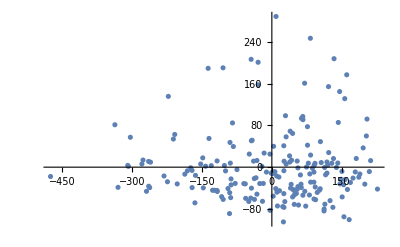

```mathematica
ListPlot[proyeccion]
```

```mathematica
FindClusters[proyeccion,4]
```

FindClusters::wrgdist: The distance function EuclideanDistance cannot be comuputed on the data.

FindClusters[{{70.801,-46.2903},{-186.961,-13.4205},{-56.2674,-59.7257},{45.6558,-42.749},{1.80262,-9.15555},{118.447,9.85975},{38.5888,9.83945},{25.7027,-50.6386},{-117.707,11.924},{74.5071,0.21694},{-49.6438,-65.7134},{15.12,-18.9454},{168.804,-29.3526},{61.3983,-14.8887},{-42.3005,51.5344},{97.52,-48.42},{-165.28,-68.3591},{162.418,-42.7287},{151.09,-56.9935},{-87.5662,-33.8876},{186.839,-19.2271},{115.497,-14.5842},{-107.895,-56.4768},{93.9452,-62.306},{-57.0475,-32.0364},{57.299,-72.5664},{25.9768,-76.9795},{25.667,40.9742},{47.7735,-44.7281},{166.192,-100.508},{11.0341,-47.8403},{154.892,-95.0461},{112.086,-83.9503},{24.8484,-104.855},{42.3522,13.2948},{2.94532,-55.5761},{113.933,-70.9468},{199.777,-32.5228},{52.6645,-50.4023},{83.3606,-28.7059},{131.148,-76.9377},{-142.321,1.78687},{2.41127,-12.0628},{83.2328,23.1659},{87.2435,-2.01814},{120.055,4.20096},{12.0332,-74.341},{81.5154,-12.9873},{125.029,-64.1324},{148.647,-23.2674},{27.8239,-66.0202},{-231.679,-16.9262},{55.9756,-37.2793},{174.45,-20.9399},{44.5935,-57.0246},{48.1489,-71.2448},{-90.5795,-48.8878},{-20.0967,-65.4075},{-90.9589,-88.9141},{112.346,-80.052},{-4.10604,25.0246},{-37.3508,-61.8112},{62.647,-32.5435},{40.1785,-40.0649},{-1.13998,-11.6069},{54.5409,-42.3725},{80.7047,-53.3396},{-60.2866,-31.532},{38.0394,21.6534},{10.3644,-16.8883},{66.7251,-53.7587},{-475.527,-17.871},{-164.04,-15.7626},{-152.913,6.04639},{-101.937,3.20737},{63.2736,-39.0381},{-269.359,-46.251},{-181.541,-7.01885},{-26.0048,-31.3997},{-104.582,-61.7148},{-43.9612,50.5502},{-330.511,-38.6732},{-45.4052,-59.2694},{-127.369,-44.2619},{-123.302,-44.2739},{-171.34,-39.1618},{72.7618,-74.644},{16.4072,-45.1047},{-117.252,-46.5893},{-224.323,-27.9496},{-11.6237,-9.40776},{-309.55,3.32918},{-203.342,-32.0853},{-260.777,9.53115},{-99.5196,-7.14382},{-264.778,10.9359},{-37.7036,-21.8513},{26.2918,11.3714},{-89.8969,47.3194},{90.5468,-60.9789},{103.9,-41.3761},{78.4147,7.61774},{-147.331,-39.6821},{-3.84303,-82.7249},{56.0009,-1.34734},{-18.4378,-31.2133},{-39.3313,11.5467},{-337.252,81.255},{-174.364,-1.20803},{-308.311,1.52963},{-78.7472,-31.1299},{-279.242,6.03691},{-44.5019,206.581},{54.4068,11.7063},{-16.5943,26.9455},{-89.1888,7.74672},{39.3721,68.8979},{-82.7027,39.5061},{-87.6336,-22.5258},{30.6567,5.98399},{128.856,7.50255},{122.15,27.9558},{102.424,-44.0482},{-130.1,2.92328},{-74.9273,-4.66309},{-88.4245,-58.3689},{92.6813,7.32815},{154.254,-33.5585},{6.51893,-8.66524},{-29.2701,157.869},{-117.871,-44.5765},{-262.499,-39.1499},{-43.8479,-40.2215},{-211.587,53.8344},{-94.2395,-40.9548},{132.416,16.49},{113.383,-0.563216},{3.77579,39.8993},{-84.5579,84.7648},{66.4989,97.0641},{29.2882,98.5356},{106.094,8.81829},{-135.058,55.0093},{90.3387,-28.741},{23.3904,-75.5416},{-264.617,-36.5582},{-48.5106,25.1084},{-208.653,62.6632},{76.6198,42.0529},{-171.445,-6.15899},{76.4676,77.5706},{8.97518,288.714},{-32.0793,-51.7041},{179.206,-9.14363},{90.4036,-9.47015},{93.2008,-38.0443},{44.5681,64.6544},{157.199,-23.7549},{-276.849,13.6574},{-148.499,17.7895},{142.772,85.6193},{-21.3259,1.3701},{-222.422,135.597},{90.9517,3.51089},{-304.015,57.26},{8.43095,-41.1055},{145.668,144.824},{30.6586,58.0737},{-29.5522,200.965},{70.4112,160.815},{204.452,92.1591},{-34.0343,-20.3122},{138.751,-0.61718},{82.7579,246.943},{41.4965,-32.8756},{189.146,-13.0934},{25.8369,-6.77116},{150.572,-8.08012},{203.054,59.7586},{181.393,16.5773},{48.4581,-53.1038},{196.207,36.9113},{209.466,-8.47119},{118.394,-11.4017},{160.89,176.962},{226.923,-41.9813},{104.368,48.9349},{156.657,131.263},{66.8381,90.9742},{-32.0359,12.74},{-104.912,190.348},{141.636,7.9387},{121.75,154.287},{133.619,207.813},{63.6679,93.4852},{146.476,-32.0776},{212.225,12.5321},{-136.906,189.335}},4]